```mathematica
Quit[]
Remove["*"]
```

total number of errors and warnings
===================================
fferr: no errors

```mathematica
FindLibrary["libcollierX"]
Needs["CollierLink`"]
Needs["X`"]
Needs["HEPMath`"]
Install["LoopTools"]
Needs["LoopTools`"]
Print[$Packages]
```

/home/kds/.Mathematica/Applications/CollierLink/LibraryResources/Linux-x86-64/libcollierX.so

Package-X v2.1.1, by Hiren H. Patel
For more information, see the

CollierLink v1.0.1, by Hiren H. Patel
For more information, see the

Eps::shdw: Symbol Eps appears in multiple contexts {HEPMath`Lorentz`,X`}; definitions in context HEPMath`Lorentz` may shadow or be shadowed by other definitions.

Dim::shdw: Symbol Dim appears in multiple contexts {HEPMath`Lorentz`,X`}; definitions in context HEPMath`Lorentz` may shadow or be shadowed by other definitions.

PaVe::shdw: Symbol PaVe appears in multiple contexts {LoopTools`,HEPMath`PaVe`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

====================================================
   FF 2.0, a package to evaluate one-loop integrals
 written by G. J. van Oldenborgh, NIKHEF-H, Amsterdam
 ====================================================
 for the algorithms used see preprint NIKHEF-H 89/17,
 'New Algorithms for One-loop Integrals', by G.J. van
 Oldenborgh and J.A.M. Vermaseren, published in 
 Zeitschrift fuer Physik C46(1990)425.
 ====================================================

LinkObject[…]

{LoopTools`,HEPMath`FeynIntegrals`,HEPMath`Kinematics`,HEPMath`PaVe`,HEPMath`Color`,HEPMath`Lorentz`,HEPMath`Tensors`,HEPMath`,Parallel`Protected`,Parallel`Developer`,Parallel`Evaluate`,GeneralUtilities`,Templating`,Parallel`Combine`,Parallel`Queue`Priority`,Parallel`Queue`FIFO`,Parallel`Queue`Interface`,Parallel`Concurrency`,Parallel`VirtualShared`,Parallel`Status`,RemoteEvaluators`WSTPServerKernels`,ProcessLink`,RemoteEvaluators`SshKernels`,RemoteEvaluators`SelfKernels`,RemoteEvaluators`LocalKernels`,RemoteEvaluators`CloudKernels`,RemoteKernelObject`,SubKernels`RemoteKernelBridge`,Parallel`Palette`,Parallel`Parallel`,SubKernels`Protected`,SubKernels`,Parallel`Kernels`,Parallel`,Parallel`Debug`Perfmon`,Parallel`Debug`,Parallel`Preferences`,X`,CollierLink`,Macros`,DocumentationSearch`Skeletonizer`,JLink`,DocumentationSearch`,GetFEKernelInit`,HighlightingCompatibility`,RemoteEvaluate`,URLUtilities`,KeychainLink`,UnitTable`,QuestionFramework`,CloudObject`CreateUUID`,CloudObjectLoader`,ResourceFunctionHelpers`,CloudDialogs`,EntityFramework`,CSGRegion`Load`,Regions`Load`,NurbsRegion`Load`,ImportExport`Load`,WebAudioSearchLoader`,NeuralNetworks`,NeuralFunctions`,NaturalLanguageProcessingLoader`,NaturalLanguage`,MobileMessaging`,Interpreter`,IntegratedServices`,IconizeLoader`,HTTPHandling`,GeoTools`,GeometrySearchLoader`,Forms`,FormNotebook`,ExternalEvaluate`,DatasetLoader`,Cryptography`,CloudExpressionLoader`,Blockchain`,Authentication`,SystemTools`,SecureShellLink`,MailLink`,IMAPLink`,ExternalStorage`,PacletManager`,WolframAppCatalog`,ResourceLocator`,PersistenceLocations`,System`,Global`}

```mathematica
Print["Trying:"]
d = 4;
str=Import["ZZZ/F1Z.txt"]

B0[1000,10,10]
C0i[cc0,0.1,0.1,1,0.1,0.100,0.200]
TraditionalForm[PVC[1,1,0,a,b,c,d,e,f]]
TraditionalForm[PVC[0,1,0,a,b,c,d,e,f]]
```

Trying:

(I*g^3*mZ^2*Pi^2*pref*(-LoopTools`C0i[cc1, s, mZ^2, mZ^2, mh1^2, mZ^2, mh2^2] + LoopTools`C0i[cc1, s, mZ^2, mZ^2, mh1^2, mZ^2, mh3^2] + LoopTools`C0i[cc1, s, mZ^2, mZ^2, mh2^2, mZ^2, mh1^2] - LoopTools`C0i[cc1, s, mZ^2, mZ^2, mh2^2, mZ^2, mh3^2] - LoopTools`C0i[cc1, s, mZ^2, mZ^2, mh3^2, mZ^2, mh1^2] + LoopTools`C0i[cc1, s, mZ^2, mZ^2, mh3^2, mZ^2, mh2^2]))/cw^3 + (I*g^3*Pi^2*pref*(LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh1^2, mh2^2, mh3^2] - LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh1^2, mh3^2, mh2^2] - LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh2^2, mh1^2, mh3^2] + LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh2^2, mh3^2, mh1^2] + LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh3^2, mh1^2, mh2^2] - LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh3^2, mh2^2, mh1^2]))/cw^3 + (I*g^3*Pi^2*pref*(-LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh1^2, mh2^2, mZ^2] + LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh1^2, mh3^2, mZ^2] + LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh1^2, mZ^2, mh2^2] - LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh1^2, mZ^2, mh3^2] + LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh2^2, mh1^2, mZ^2] - LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh2^2, mh3^2, mZ^2] - LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh2^2, mZ^2, mh1^2] + LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh2^2, mZ^2, mh3^2] - LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh3^2, mh1^2, mZ^2] + LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh3^2, mh2^2, mZ^2] + LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh3^2, mZ^2, mh1^2] - LoopTools`C0i[cc001, s, mZ^2, mZ^2, mh3^2, mZ^2, mh2^2] - LoopTools`C0i[cc001, s, mZ^2, mZ^2, mZ^2, mh1^2, mh2^2] + LoopTools`C0i[cc001, s, mZ^2, mZ^2, mZ^2, mh1^2, mh3^2] + LoopTools`C0i[cc001, s, mZ^2, mZ^2, mZ^2, mh2^2, mh1^2] - LoopTools`C0i[cc001, s, mZ^2, mZ^2, mZ^2, mh2^2, mh3^2] - LoopTools`C0i[cc001, s, mZ^2, mZ^2, mZ^2, mh3^2, mh1^2] + LoopTools`C0i[cc001, s, mZ^2, mZ^2, mZ^2, mh3^2, mh2^2]))/cw^3

1/cw^3 ⅈ π^2 g^3 pref (C0i(cc001,s,mZ^2,mZ^2,mh1^2,mh2^2,mh3^2)-C0i(cc001,s,mZ^2,mZ^2,mh1^2,mh3^2,mh2^2)-C0i(cc001,s,mZ^2,mZ^2,mh2^2,mh1^2,mh3^2)+C0i(cc001,s,mZ^2,mZ^2,mh2^2,mh3^2,mh1^2)+C0i(cc001,s,mZ^2,mZ^2,mh3^2,mh1^2,mh2^2)-C0i(cc001,s,mZ^2,mZ^2,mh3^2,mh2^2,mh1^2))+1/cw^3 ⅈ π^2 g^3 pref (-C0i(cc001,s,mZ^2,mZ^2,mh1^2,mh2^2,mZ^2)+C0i(cc001,s,mZ^2,mZ^2,mh1^2,mZ^2,mh2^2)+C0i(cc001,s,mZ^2,mZ^2,mh2^2,mh1^2,mZ^2)-C0i(cc001,s,mZ^2,mZ^2,mh2^2,mZ^2,mh1^2)-C0i(cc001,s,mZ^2,mZ^2,mZ^2,mh1^2,mh2^2)+C0i(cc001,s,mZ^2,mZ^2,mZ^2,mh2^2,mh1^2)+C0i(cc001,s,mZ^2,mZ^2,mh1^2,mh3^2,mZ^2)-C0i(cc001,s,mZ^2,mZ^2,mh1^2,mZ^2,mh3^2)-C0i(cc001,s,mZ^2,mZ^2,mh3^2,mh1^2,mZ^2)+C0i(cc001,s,mZ^2,mZ^2,mh3^2,mZ^2,mh1^2)+C0i(cc001,s,mZ^2,mZ^2,mZ^2,mh1^2,mh3^2)-C0i(cc001,s,mZ^2,mZ^2,mZ^2,mh3^2,mh1^2)-C0i(cc001,s,mZ^2,mZ^2,mh2^2,mh3^2,mZ^2)+C0i(cc001,s,mZ^2,mZ^2,mh2^2,mZ^2,mh3^2)+C0i(cc001,s,mZ^2,mZ^2,mh3^2,mh2^2,mZ^2)-C0i(cc001,s,mZ^2,mZ^2,mh3^2,mZ^2,mh2^2)-C0i(cc001,s,mZ^2,mZ^2,mZ^2,mh2^2,mh3^2)+C0i(cc001,s,mZ^2,mZ^2,mZ^2,mh3^2,mh2^2))+1/cw^3 ⅈ π^2 g^3 mZ^2 pref (-C0i(cc1,s,mZ^2,mZ^2,mh1^2,mZ^2,mh2^2)+C0i(cc1,s,mZ^2,mZ^2,mh2^2,mZ^2,mh1^2)+C0i(cc1,s,mZ^2,mZ^2,mh1^2,mZ^2,mh3^2)-C0i(cc1,s,mZ^2,mZ^2,mh3^2,mZ^2,mh1^2)-C0i(cc1,s,mZ^2,mZ^2,mh2^2,mZ^2,mh3^2)+C0i(cc1,s,mZ^2,mZ^2,mh3^2,mZ^2,mh2^2))

0

-4.79482+3.07812 ⅈ

-3.93958-7.17275 ⅈ

C_(0,0,1)(a,b,c;4,e,f)

C_1(a,b,c;4,e,f)

```mathematica
m = 10^(-3);
mZ=91.187*m;
m1=125*m;
m2=500*m;
v=246.22*m;
m3=(v^2+m2^2)^(0.5);

LT[q_,mi_,mj_,mk_]:=-C0i[cc001,q^2,mZ^2,mZ^2,mi^2,mj^2,mk^2]+C0i[cc001,q^2,mZ^2,mZ^2,mi^2,mj^2,mZ^2]+C0i[cc001,q^2,mZ^2,mZ^2,mZ^2,mj^2,mk^2]+C0i[cc001,q^2,mZ^2,mZ^2,mi^2,mZ^2,mk^2]-mZ^2 C0i[cc1,q^2,mZ^2,mZ^2,mi^2,mZ^2,mk^2];
CPLT[q_,mi_,mj_,mk_]:=LT[q,mi,mj,mk]-LT[q,mi,mk,mj]-LT[q,mj,mi,mk]+LT[q,mj,mk,mi]+LT[q,mk,mi,mj]-LT[q,mk,mj,mi];

CP[q_,mi_,mj_,mk_]:=-PVC[1,1,0,mZ^2,mZ^2,q^2,mi^2,mj^2,mk^2]+PVC[1,1,0,mZ^2,mZ^2,q^2,mi^2,mj^2,mZ^2]+PVC[1,1,0,mZ^2,mZ^2,q^2,mZ^2,mj^2,mk^2]+PVC[1,1,0,mZ^2,mZ^2,q^2,mi^2,mZ^2,mk^2]-mZ^2 PVC[0,1,0,mZ^2,mZ^2,q^2,mi^2,mZ^2,mk^2];
PV[q_,mi_,mj_,mk_]:=CP[q,mi,mj,mk]-CP[q,mi,mk,mj]-CP[q,mj,mi,mk]+CP[q,mj,mk,mi]+CP[q,mk,mi,mj]-CP[q,mk,mj,mi];

CP1[q_,mi_,mj_,mk_]:=
-PVC[1,1,0,q^2,mZ^2,mZ^2,mi^2,mj^2,mk^2]-PVC[1,1,0,q^2,mZ^2,mZ^2,mj^2,mk^2,mi^2]-PVC[1,1,0,q^2,mZ^2,mZ^2,mk^2,mi^2,mj^2]+
PVC[1,1,0,q^2,mZ^2,mZ^2,mi^2,mk^2,mj^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mk^2,mj^2,mi^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mj^2,mi^2,mk^2]+
PVC[1,1,0,q^2,mZ^2,mZ^2,mi^2,mj^2,mZ^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mj^2,mk^2,mZ^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mk^2,mi^2,mZ^2]-
PVC[1,1,0,q^2,mZ^2,mZ^2,mj^2,mi^2,mZ^2]-PVC[1,1,0,q^2,mZ^2,mZ^2,mi^2,mk^2,mZ^2]-PVC[1,1,0,q^2,mZ^2,mZ^2,mk^2,mj^2,mZ^2]+
PVC[1,1,0,q^2,mZ^2,mZ^2,mZ^2,mj^2,mi^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mZ^2,mi^2,mk^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mZ^2,mk^2,mj^2]-
PVC[1,1,0,q^2,mZ^2,mZ^2,mZ^2,mi^2,mj^2]-PVC[1,1,0,q^2,mZ^2,mZ^2,mZ^2,mj^2,mk^2]-PVC[1,1,0,q^2,mZ^2,mZ^2,mZ^2,mk^2,mi^2]+
PVC[1,1,0,q^2,mZ^2,mZ^2,mj^2,mZ^2,mi^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mi^2,mZ^2,mk^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mk^2,mZ^2,mj^2]-
PVC[1,1,0,q^2,mZ^2,mZ^2,mi^2,mZ^2,mj^2]-PVC[1,1,0,q^2,mZ^2,mZ^2,mj^2,mZ^2,mk^2]-PVC[1,1,0,q^2,mZ^2,mZ^2,mk^2,mZ^2,mi^2]-
mZ^2(PVC[0,1,0,q^2,mZ^2,mZ^2,mj^2,mZ^2,mi^2]+PVC[0,1,0,q^2,mZ^2,mZ^2,mi^2,mZ^2,mk^2]+PVC[0,1,0,q^2,mZ^2,mZ^2,mk^2,mZ^2,mj^2]-
PVC[0,1,0,q^2,mZ^2,mZ^2,mi^2,mZ^2,mj^2]-PVC[0,1,0,q^2,mZ^2,mZ^2,mj^2,mZ^2,mk^2]-PVC[0,1,0,q^2,mZ^2,mZ^2,mk^2,mZ^2,mi^2]);
Delt[q_,mi_,mj_,mk_]:=PV[q,mi,mj,mk]-CPLT[q,mi,mj,mk];
Print["Delta:"]
Abs[Delt[4,m1,m2,m3]]
A2=C0i[cc001,2^2,mZ^2,mZ^2,m1^2,m2^2,m3^2];
A1=PVC[1,1,0,mZ^2,mZ^2,4,0.125^2,0.5^2,(0.5^2+0.246^2)];
Abs[A2-A1]
Abs[PV[2,m1,m2,m3]];
Abs[PV[2/m,m1/m,m2/m,m3/m]];

Abs[CPLT[2/m,m1/m,m2/m,m3/m]];
Abs[CPLT[2,m1,m2,m3]];
Print["----"]
N[PVC[1,1,0,2^2,mZ^2,mZ^2,m1^2,m2^2,m3^2]]
N[PVC[0,1,0,1000^2,1000^2,2000^2,1000^2,2000^2,3000^2]]
Print["----"]
N[C0i[cc1,2^2,mZ^2,mZ^2,m1^2,m2^2,m3^2]]
N[C0i[cc1,2000^2,(mZ/m)^2,(mZ/m)^2,(m1/m)^2,(m2/m)^2,(m3/m)^2]]
(*Они зависят от масштаба*)
```

Delta:

0.0000138818

0.06947

----

-0.127799-0.234459 ⅈ

7.61305×10^-15+0. ⅈ

----

-0.100704+0.585042 ⅈ

-1.00704×10^-7+5.85042×10^-7 ⅈ

-Graphics-

Prefactor:

0.00783683

1/(16 π^2 cw^3 (1-mZ^2))g^3 mZ^2 cos(π/22) (1/2 (1/2 √3 sin(π/7)-1/2 sin(π/22) cos(π/7))-1/2 √3 (1/2 sin(π/7)+1/2 √3 sin(π/22) cos(π/7))) (1/2 (-1/2 sin(π/22) sin(π/7)-1/2 √3 cos(π/7))+1/2 √3 (1/2 cos(π/7)-1/2 √3 sin(π/22) sin(π/7)))

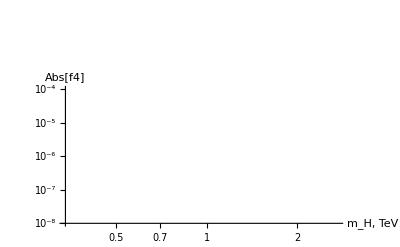

```mathematica
b= 1;
p0=LogPlot[Abs[PV[x,m1,b,√((b)^2+v^2)]],{x,0.200,1.60},PlotStyle->{Red,Dashed},PlotLabel->"Xcollier fig5"];
p3=LogPlot[Abs[CPLT[x,m1,b,√((b)^2+v^2)]],{x,0.200,1.60},PlotLabel->"LoopTools fig5"];
Show[p3,p0]
(*P = LogPlot[Abs[PV[x,m1,b,√((b)^2+v^2)]]-Abs[CPLT[x,m1,b,√((b)^2+v^2)]],{x,0.200,1.60},PlotLabel->"LoopTools vs Xcollier"]
p1 = LogLogPlot[Re[CPLT[1.000,m1,x,√((x)^2+v^2)]], {x, 0.100, 10.000},PlotLabel->"LoopTools Re fig7",PlotStyle->{Red,Dashed}]
p2 = LogLogPlot[Im[CPLT[1.000,m1,x,√((x)^2+v^2)]], {x, 0.100, 10.000},PlotLabel->"LoopTools Im fig7",PlotStyle->{Dotted}]*)
α2 = π/22; (* Lightest Higgs is a pure scalar*)
α1 = π/3;
α3 = π/7;

x1[a1_,a2_,a3_] := (Cos[a1]*Cos[a2]*Cos[a1] + Sin[a1]*Cos[a2]*Sin[a1]);
x2[a1_,a2_,a3_] :=  (-(Sin[a1]*Cos[a3] + Cos[a1]*Sin[a2]*Sin[a3])*Cos[a1] + (Cos[a1]*Cos[a3] - Sin[a1]*Sin[a2] *Sin[a3])*Sin[a1]);
x3[a1_,a2_,a3_] := ((-Cos[a1] *Sin[a2]* Cos[a3] + Sin[a1] *Sin[a3])*Cos[a1] -(Sin[a1] *Sin[a2] *Cos[a3] + Cos[a1]* Sin[a3])*Sin[a1]);
Print["Prefactor:"]
prefactor[a1_,a2_,a3_] := x1[a1,a2,a3] x2[a1,a2,a3] x3[a1,a2,a3];
N[prefactor[α1,α2,α3]]
pref1 =mZ^2/(b^2-mZ^2)g^3/(16 π^2 cw^3)prefactor[α1,α2,α3]
label1 = Text[Style["p=" <> ToString[p] <> " TeV", FontSize -> 14, FontFamily -> "Arial", FontWeight -> Bold, 
       Background -> LightGray], {0, 0}];
data = Table[{x, N[Abs[CPLT[0.5,m1,x,√((x)^2+v^2)]*pref1]]}, {x, 0.1, 10,0.01}] // N;
l = ListLogLogPlot[data,
PlotMarkers -> Automatic,
Epilog -> label1, 
AxesLabel -> {"m_H, TeV", "Abs[f4]"}, 
PlotRange -> {10^-8,10^-4},
GridLines -> Automatic];

Show[l]
```